## Create Config File

### Parameter names and benchmark values

```mathematica
SetDirectory[NotebookDirectory[]];
params={"INDEX","CYCLES_PER_SIMULATION","SIMULATIONS","PRINT_DEBUG","PATH","AGENT_FIRM_CAPITAL_Q","AGENT_FIRM_CAPITAL_NW","AGENT_FIRM_CAPITAL_MARGIN","AGENT_FIRM_CAPITAL_RD_PROPENSITY","AGENT_FIRM_CAPITAL_FRACTION_X","AGENT_FIRM_CAPITAL_Z_IN","AGENT_FIRM_CAPITAL_Z_IM","AGENT_FIRM_CAPITAL_PRODUCTIVITY_A_MIN","AGENT_FIRM_CAPITAL_PRODUCTIVITY_A_MAX","AGENT_FIRM_CAPITAL_PRODUCTIVITY_B_MIN","AGENT_FIRM_CAPITAL_PRODUCTIVITY_B_MAX","AGENT_FIRM_CAPITAL_BROCHURES","AGENT_FIRM_CONSUMER_Q","AGENT_FIRM_CONSUMER_STOCK_SPARE","AGENT_FIRM_CONSUMER_MARGIN","AGENT_FIRM_CONSUMER_CAPITAL_INTENSITY","AGENT_FIRM_CONSUMER_NW","AGENT_FIRM_CONSUMER_PAYBACK_PERIOD","AGENT_FIRM_CONSUMER_COMPETITIVITY_PRICE_W1","AGENT_FIRM_CONSUMER_COMPETITIVITY_UNFILLED_W2","AGENT_FIRM_CONSUMER_OBSOLETE","COMPETITIVITY_MARKETSHARE","AGENT_PERSON","AGENT_PERSON_EXPEND","AGENT_GOVERNMENT_EMPLOYEE_TAX","AGENT_GOVERNMENT_FIRM_TAX","AGENT_GOVERNMENT_UNEMPLOYED_WAGE","WORLD_WAGE","PS1","PS2"};
benchmark={0,200,20,"FALSE","",2,1000,1.5,0.04,0.5,0.3,0.3,5,15,5,10,10,4,100,1.5,0.4,4000,3,1,1,20,1,10,0.8,0.1,0.1,0.4,30,0.5,0.5};(*benchmark[[{6,18,28}]]=!{20,40,150}*)
symbols=ToString[#]&/@{i,T,L,"","",F1,"",μ1,ν,ξ,ζ1,ζ2,"","","","",γ,F2,"",μ2,κ,"",b,ω1,ω2,η,"","#","",Te,Tf,u,w,ψ1,ψ2};
```

```mathematica
SetDirectory["/home/miglesia/Desktop"]
```

/home/miglesia/Desktop

```mathematica
Export["paramtable.png",Delete[Join[{params},{benchmark},{symbols}]ᵀ,{{4},{5},{13},{14},{15},{16}}]//TableForm]
```

paramtable.png

## Explorations in reduced parameter spaces.

### Initial conditions experiment

```mathematica
n=20;
f=Table[benchmark,{i,1,n}];
f[[All,1]]=Table[i-1,{i,1,n}];
f[[All,33]]=f[[All,33]]*RandomReal[{0.3,3},n]//Round;
f[[All,7]]=f[[All,7]]*RandomReal[{0.3,3},n]//Round;
f[[All,22]]=f[[All,22]]*RandomReal[{0.3,3},n]//Round;
Export["SimConfig.csv",Join[{params},f]];
```

### Fiscal Policy experiment

```mathematica
n=300;
f=Table[benchmark,{i,1,n}];
f[[All,1]]=Table[i-1,{i,1,n}];
f[[All,30]]=RandomReal[{0,1},n];
f[[All,31]]=RandomReal[{0,1},n];
f[[All,32]]=RandomReal[{0,1},n];
Export["SimConfig.csv",Join[{params},f]];
```

### Wage updates experiment

```mathematica
benchmark[[{6,18,28}]]={2,4,10}
```

{2,4,10}

```mathematica
f=Table[benchmark,{i,1,121}];
f[[All,{34,35}]]=SortBy[Flatten[Table[Table[{i,j},{j,0,1,0.1}],{i,0,1,0.1}],1],Norm];
n=Length[%]
f[[All,1]]=Table[i-1,{i,1,n}];
Export["SimConfig.csv",Join[{params},f]];
```

121

### Innovation sector experiment

```mathematica
n=500;
f=Table[benchmark,{i,1,n}];
f[[All,1]]=Table[i-1,{i,1,n}];
f[[All,9]]=RandomReal[{0,0.9},n];
f[[All,23]]=RandomReal[{1,5},n]^2//Round;
f[[All,26]]=RandomReal[{1,8},n]^2//Round;
Export["SimConfig.csv",Join[{params},f]];
```

```mathematica
params[[{9,23,26}]]
```

{AGENT_FIRM_CAPITAL_RD_PROPENSITY,AGENT_FIRM_CONSUMER_PAYBACK_PERIOD,AGENT_FIRM_CONSUMER_OBSOLETE}

```mathematica
f[[All,{9,23,26}]]//TableForm
```

0.214822 | 23 | 2
0.470471 | 19 | 9
0.286171 | 5 | 15
0.364357 | 14 | 16
0.882094 | 8 | 54
0.780859 | 5 | 14
0.198337 | 2 | 8
0.0926589 | 7 | 5
0.384677 | 2 | 5
0.0462522 | 5 | 13
0.171844 | 13 | 4
0.79901 | 24 | 52
0.630176 | 14 | 7
0.854203 | 24 | 32
0.0440396 | 11 | 35
0.667678 | 21 | 38
0.140728 | 2 | 3
0.380377 | 15 | 5
0.512297 | 2 | 11
0.0488727 | 5 | 11
0.280242 | 21 | 29
0.398324 | 17 | 3
0.594891 | 4 | 52
0.769762 | 24 | 27
0.712822 | 25 | 31
0.319264 | 21 | 6
0.7584 | 17 | 21
0.146363 | 2 | 2
0.23293 | 3 | 4
0.276883 | 22 | 53
0.0188077 | 25 | 57
0.10038 | 14 | 39
0.261116 | 22 | 43
0.739154 | 9 | 2
0.565933 | 5 | 41
0.701398 | 4 | 35
0.820954 | 3 | 26
0.511959 | 12 | 14
0.589427 | 2 | 2
0.333763 | 6 | 11
0.75801 | 10 | 19
0.193754 | 8 | 43
0.440125 | 5 | 13
0.668801 | 1 | 2
0.439507 | 2 | 26
0.796702 | 12 | 16
0.267215 | 23 | 52
0.441205 | 2 | 45
0.862427 | 2 | 3
0.221119 | 21 | 57
0.672158 | 17 | 33
0.667161 | 10 | 36
0.516202 | 2 | 62
0.700414 | 5 | 15
0.272892 | 16 | 17
0.826756 | 3 | 38
0.682662 | 21 | 45
0.430736 | 14 | 34
0.308933 | 2 | 2
0.188 | 9 | 42
0.809502 | 21 | 10
0.24506 | 3 | 45
0.330138 | 19 | 3
0.785153 | 10 | 2
0.648781 | 11 | 46
0.808208 | 15 | 1
0.504864 | 4 | 7
0.753612 | 15 | 17
0.88975 | 19 | 20
0.406842 | 3 | 13
0.467354 | 25 | 10
0.503483 | 8 | 23
0.835889 | 8 | 13
0.318332 | 4 | 16
0.0410952 | 6 | 41
0.896432 | 5 | 7
0.145366 | 16 | 27
0.520563 | 14 | 57
0.115185 | 2 | 22
0.643483 | 3 | 7
0.731302 | 17 | 13
0.348043 | 1 | 12
0.552541 | 10 | 10
0.562181 | 7 | 18
0.139188 | 11 | 15
0.431819 | 20 | 18
0.685218 | 6 | 32
0.281412 | 5 | 1
0.0229145 | 20 | 46
0.885583 | 5 | 22
0.171963 | 3 | 5
0.380527 | 21 | 43
0.792589 | 3 | 11
0.610898 | 7 | 5
0.122247 | 2 | 42
0.825751 | 18 | 6
0.299766 | 10 | 6
0.27941 | 8 | 56
0.113076 | 8 | 5
0.510432 | 8 | 12
0.26746 | 24 | 55
0.899911 | 7 | 40
0.161981 | 5 | 16
0.257432 | 5 | 42
0.404482 | 12 | 5
0.166395 | 11 | 53
0.532698 | 19 | 63
0.0732482 | 11 | 8
0.852886 | 2 | 31
0.634213 | 17 | 5
0.886678 | 23 | 48
0.462873 | 17 | 53
0.277005 | 17 | 25
0.252775 | 1 | 19
0.128 | 1 | 2
0.598758 | 19 | 56
0.560851 | 6 | 11
0.233227 | 17 | 1
0.106329 | 5 | 47
0.708367 | 9 | 16
0.0347866 | 24 | 2
0.182314 | 3 | 17
0.878364 | 17 | 22
0.779335 | 2 | 28
0.25937 | 24 | 51
0.42326 | 10 | 3
0.291878 | 16 | 23
0.597777 | 23 | 5
0.212289 | 17 | 2
0.739186 | 17 | 40
0.0152989 | 7 | 2
0.793685 | 8 | 24
0.766617 | 4 | 10
0.0850057 | 14 | 14
0.17325 | 4 | 62
0.0728714 | 18 | 19
0.438417 | 12 | 2
0.306492 | 7 | 5
0.594485 | 9 | 7
0.449131 | 11 | 11
0.383594 | 22 | 58
0.696375 | 1 | 9
0.0232651 | 22 | 45
0.746246 | 4 | 33
0.231474 | 18 | 2
0.156741 | 1 | 7
0.772392 | 5 | 14
0.0482949 | 6 | 3
0.175592 | 3 | 22
0.779835 | 13 | 12
0.28354 | 18 | 4
0.098131 | 16 | 11
0.354067 | 2 | 12
0.347867 | 10 | 37
0.596825 | 5 | 63
0.416217 | 9 | 11
0.317339 | 18 | 28
0.727491 | 16 | 55
0.165445 | 6 | 2
0.238395 | 15 | 22
0.817228 | 11 | 9
0.780499 | 8 | 3
0.208452 | 8 | 19
0.314314 | 7 | 6
0.784404 | 4 | 9
0.635727 | 5 | 11
0.0801911 | 4 | 24
0.649746 | 1 | 7
0.796816 | 17 | 4
0.680953 | 2 | 15
0.784584 | 16 | 41
0.0234235 | 4 | 11
0.230511 | 22 | 61
0.800739 | 14 | 8
0.835434 | 5 | 2
0.751085 | 4 | 34
0.246277 | 16 | 64
0.328558 | 21 | 4
0.611714 | 4 | 58
0.695024 | 4 | 28
0.41622 | 19 | 59
0.777593 | 19 | 42
0.517629 | 12 | 60
0.364391 | 16 | 2
0.353364 | 14 | 44
0.55486 | 25 | 52
0.340521 | 18 | 54
0.885628 | 2 | 63
0.105281 | 7 | 3
0.589065 | 5 | 37
0.155459 | 2 | 14
0.113026 | 3 | 8
0.408561 | 12 | 3
0.227685 | 20 | 20
0.699504 | 6 | 30
0.211379 | 23 | 28
0.431973 | 10 | 20
0.399604 | 22 | 50
0.618543 | 13 | 6
0.609158 | 24 | 56
0.116328 | 15 | 36
0.533906 | 16 | 46
0.1852 | 3 | 2
0.261585 | 15 | 45
0.136021 | 2 | 6
0.189334 | 19 | 29
0.323541 | 23 | 56
0.104214 | 7 | 8
0.844395 | 7 | 7
0.175633 | 1 | 57
0.147801 | 22 | 32
0.11445 | 21 | 9
0.567516 | 10 | 41
0.296425 | 6 | 21
0.771817 | 12 | 63
0.262077 | 11 | 19
0.147725 | 12 | 7
0.613777 | 3 | 4
0.524529 | 4 | 56
0.284752 | 4 | 14
0.198944 | 15 | 51
0.0120846 | 9 | 1
0.634164 | 7 | 2
0.103842 | 5 | 4
0.653537 | 12 | 5
0.0883193 | 6 | 1
0.574721 | 20 | 44
0.214975 | 21 | 2
0.657815 | 10 | 19
0.733942 | 13 | 17
0.436449 | 17 | 26
0.103764 | 11 | 28
0.519184 | 9 | 41
0.246887 | 2 | 6
0.291414 | 5 | 10
0.179911 | 15 | 47
0.61118 | 1 | 11
0.141954 | 13 | 3
0.181744 | 16 | 4
0.287882 | 2 | 30
0.0175335 | 7 | 60
0.519488 | 7 | 49
0.695215 | 8 | 32
0.52798 | 20 | 37
0.4476 | 4 | 30
0.669834 | 12 | 24
0.728781 | 14 | 46
0.629899 | 9 | 27
0.875806 | 4 | 61
0.376003 | 4 | 35
0.138277 | 4 | 20
0.279467 | 24 | 19
0.485792 | 9 | 20
0.508283 | 21 | 13
0.827576 | 24 | 13
0.237939 | 2 | 2
0.109322 | 5 | 39
0.307725 | 3 | 3
0.190828 | 10 | 27
0.25233 | 13 | 40
0.707716 | 11 | 15
0.888779 | 19 | 3
0.860746 | 16 | 62
0.749083 | 6 | 17
0.615714 | 7 | 29
0.739906 | 4 | 10
0.700682 | 20 | 35
0.0726037 | 24 | 20
0.653607 | 14 | 42
0.185251 | 6 | 7
0.486929 | 9 | 8
0.116856 | 16 | 28
0.267391 | 24 | 24
0.245093 | 19 | 19
0.282401 | 19 | 9
0.197185 | 2 | 57
0.693853 | 22 | 23
0.459778 | 3 | 6
0.580179 | 4 | 45
0.602947 | 6 | 23
0.138538 | 12 | 20
0.269924 | 5 | 53
0.42469 | 16 | 4
0.557729 | 3 | 32
0.32832 | 20 | 45
0.0501243 | 2 | 14
0.694343 | 20 | 52
0.18092 | 2 | 25
0.447402 | 15 | 11
0.133918 | 15 | 3
0.318534 | 11 | 9
0.565703 | 21 | 33
0.651952 | 1 | 48
0.876619 | 24 | 44
0.0169633 | 15 | 11
0.670007 | 4 | 5
0.481262 | 8 | 16
0.696209 | 5 | 14
0.462851 | 3 | 37
0.0922327 | 1 | 6
0.825942 | 2 | 7
0.476317 | 18 | 38
0.244446 | 1 | 1
0.457516 | 12 | 11
0.680055 | 25 | 60
0.236757 | 6 | 16
0.748794 | 5 | 50
0.333801 | 1 | 47
0.359979 | 5 | 48
0.151406 | 7 | 19
0.115774 | 12 | 3
0.724025 | 12 | 2
0.431738 | 4 | 33
0.247995 | 11 | 33
0.124604 | 9 | 18
0.44853 | 2 | 1
0.187844 | 2 | 3
0.481064 | 8 | 22
0.239294 | 7 | 18
0.0531401 | 10 | 34
0.834901 | 2 | 25
0.268102 | 25 | 2
0.455938 | 24 | 8
0.793241 | 11 | 1
0.0928561 | 3 | 54
0.592635 | 1 | 34
0.0123477 | 3 | 16
0.851947 | 8 | 51
0.811739 | 3 | 12
0.624118 | 1 | 25
0.613018 | 10 | 28
0.0658492 | 4 | 17
0.460972 | 18 | 10
0.551595 | 19 | 22
0.825966 | 19 | 5
0.713991 | 23 | 24
0.201397 | 10 | 25
0.381582 | 3 | 18
0.37158 | 19 | 35
0.626272 | 15 | 21
0.104737 | 2 | 6
0.703052 | 5 | 5
0.117877 | 6 | 56
0.363404 | 6 | 19
0.370118 | 2 | 55
0.606329 | 22 | 5
0.614036 | 10 | 11
0.553229 | 20 | 21
0.194268 | 20 | 32
0.867371 | 7 | 37
0.370097 | 9 | 41
0.719764 | 17 | 6
0.198102 | 18 | 48
0.535172 | 21 | 46
0.46733 | 21 | 44
0.672729 | 10 | 6
0.160327 | 2 | 14
0.245076 | 1 | 2
0.333829 | 8 | 15
0.882383 | 3 | 3
0.721735 | 8 | 26
0.888052 | 11 | 41
0.25258 | 6 | 4
0.421382 | 8 | 29
0.441187 | 24 | 32
0.857063 | 2 | 1
0.395145 | 16 | 34
0.246887 | 4 | 1
0.409548 | 8 | 6
0.096584 | 14 | 8
0.215292 | 2 | 33
0.811968 | 11 | 21
0.0358189 | 4 | 42
0.643965 | 1 | 20
0.438308 | 8 | 36
0.0776116 | 3 | 16
0.418023 | 17 | 10
0.24303 | 4 | 53
0.571088 | 4 | 28
0.672338 | 5 | 52
0.829445 | 16 | 37
0.169225 | 16 | 17
0.252587 | 22 | 32
0.790481 | 8 | 2
0.675905 | 17 | 17
0.48736 | 8 | 6
0.449844 | 7 | 37
0.0770703 | 1 | 38
0.313169 | 4 | 59
0.159728 | 7 | 10
0.662345 | 3 | 42
0.409944 | 15 | 7
0.127385 | 7 | 8
0.075077 | 1 | 11
0.237874 | 21 | 10
0.273644 | 13 | 3
0.5994 | 4 | 9
0.677625 | 4 | 2
0.755322 | 3 | 39
0.629745 | 3 | 50
0.00751693 | 9 | 5
0.38459 | 4 | 44
0.330257 | 24 | 19
0.247649 | 15 | 3
0.630719 | 2 | 54
0.83475 | 22 | 51
0.717207 | 9 | 10
0.542649 | 16 | 22
0.612707 | 13 | 3
0.0203081 | 18 | 14
0.652221 | 2 | 62
0.100883 | 9 | 18
0.596718 | 4 | 45
0.878512 | 3 | 40
0.36726 | 5 | 8
0.599495 | 23 | 24
0.570176 | 2 | 27
0.312101 | 6 | 34
0.237878 | 9 | 50
0.138955 | 6 | 10
0.687489 | 5 | 2
0.829628 | 13 | 13
0.307194 | 12 | 2
0.618226 | 3 | 5
0.240203 | 5 | 47
0.794346 | 14 | 3
0.369643 | 21 | 12
0.084861 | 1 | 12
0.874717 | 8 | 1
0.383658 | 15 | 6
0.00970843 | 23 | 40
0.745839 | 19 | 17
0.622322 | 5 | 6
0.0443365 | 8 | 9
0.521079 | 3 | 61
0.238006 | 6 | 63
0.156354 | 23 | 49
0.228017 | 6 | 45
0.781213 | 25 | 43
0.34465 | 15 | 25
0.194626 | 4 | 25
0.408664 | 3 | 63
0.355979 | 8 | 27
0.465894 | 21 | 33
0.621483 | 6 | 27
0.386732 | 23 | 57
0.685682 | 5 | 9
0.69712 | 6 | 3
0.130089 | 11 | 40
0.484176 | 25 | 15
0.701147 | 10 | 34
0.25951 | 2 | 5
0.424745 | 21 | 10
0.417605 | 1 | 17
0.00500966 | 14 | 9
0.859453 | 8 | 20
0.756767 | 16 | 9
0.0505239 | 21 | 3
0.224645 | 5 | 39
0.0128995 | 16 | 37
0.758266 | 23 | 29
0.860167 | 11 | 27
0.844094 | 4 | 2
0.590438 | 4 | 11
0.49139 | 5 | 52
0.281612 | 17 | 6
0.764699 | 3 | 4
0.515075 | 14 | 62
0.0333922 | 14 | 7
0.897151 | 4 | 55
0.128533 | 6 | 11
0.236063 | 11 | 6
0.372693 | 18 | 41
0.15592 | 9 | 37
0.402924 | 5 | 55
0.215315 | 18 | 14
0.238145 | 17 | 2
0.523735 | 20 | 5
0.286253 | 1 | 22
0.416906 | 10 | 5
0.429216 | 9 | 11
0.509973 | 1 | 11
0.212708 | 3 | 13
0.730446 | 20 | 13
0.409059 | 21 | 3
0.159942 | 21 | 29
0.154733 | 1 | 41
0.357178 | 7 | 57
0.889309 | 15 | 44
0.570897 | 9 | 56
0.011604 | 15 | 1
0.5511 | 21 | 33
0.158242 | 10 | 8
0.142827 | 12 | 21
0.222624 | 19 | 15
0.677937 | 5 | 1
0.586038 | 9 | 4
0.645037 | 9 | 36
0.21105 | 2 | 54
0.62533 | 17 | 29

### Population sizes experiment

```mathematica
n=10;
f=Table[benchmark,{i,1,n}];
f[[All,1]]=Table[i-1,{i,1,n}];
f[[All,6]]=f[[All,6]]*RandomReal[{0.3,5},n]//Round;
f[[All,18]]=f[[All,18]]*RandomReal[{0.1,4},n]//Round;
f[[All,28]]=f[[All,28]]*RandomReal[{0.1,2},n]//Round;
Export["SimConfig.csv",Join[{params},f]];
```

```mathematica
m=10;
t=Tuples[Range[m],{3}];
t=Tuples[Range[m],{3}][[Position[Tuples[Range[m],{3}],_?(#[[1]]+#[[2]]<=#[[3]]&)]//Flatten]]//Quiet;
(*p=RandomChoice[t,n];*)
p=t;
n=Length[p]
f=Table[benchmark,{i,1,n}];
f[[All,1]]=Table[i-1,{i,1,n}];
f[[All,6]]=p[[All,1]];
f[[All,18]]=p[[All,2]];
f[[All,28]]=p[[All,3]];
Export["SimConfig.csv",Join[{params},f]];
```

165

```mathematica
n=1500;
m=50;
t=Tuples[Range[m],{3}][[Position[Tuples[Range[m],{3}],_?(#[[1]]+#[[2]]<=#[[3]]&)]//Flatten]]//Quiet;
Length[t]
p=RandomChoice[t,n];
f=Table[benchmark,{i,1,n}];
f[[All,1]]=IntegerString[#,10,4]&/@Range[n];
f[[All,6]]=p[[All,1]];
f[[All,18]]=p[[All,2]];
f[[All,28]]=p[[All,3]];
(*Export["SimConfig.csv",Join[{params},f]];*)
```

Part::partd: Part specification List ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification List ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification List ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

20825

## Exploration of differentials

```mathematica
chosenParams=Position[params,#]&/@{"AGENT_FIRM_CAPITAL_Q","AGENT_FIRM_CAPITAL_RD_PROPENSITY","AGENT_FIRM_CONSUMER_Q","AGENT_FIRM_CONSUMER_PAYBACK_PERIOD","AGENT_FIRM_CONSUMER_OBSOLETE","AGENT_PERSON","AGENT_GOVERNMENT_EMPLOYEE_TAX","AGENT_GOVERNMENT_FIRM_TAX","AGENT_GOVERNMENT_UNEMPLOYED_WAGE","WORLD_WAGE","PS1","PS2"}//Flatten;
P=Length[chosenParams];
areInteger=Position[params,#]&/@{"AGENT_FIRM_CAPITAL_Q","AGENT_FIRM_CONSUMER_PAYBACK_PERIOD","AGENT_FIRM_CONSUMER_OBSOLETE","AGENT_FIRM_CONSUMER_Q","WORLD_WAGE","AGENT_PERSON"}//Flatten;
```

```mathematica
f=Table[benchmark,{i,1+4P}];f[[All,1]]=Range[1+4P]-1;
t={0.9,0.99,1.01,1.1};
T=Length[t];
Do[f[[1+(p-1)T;;p T,chosenParams[[p]]]]=t f[[1+(p-1)T;;p T,chosenParams[[p]]]],{p,P}]
f[[All,areInteger]]=f[[All,areInteger]]//Round;
Export["SimConfig.csv",Join[{params},f]];
```

```mathematica
(*Join[{params[[chosenParams]]},
f[[All,chosenParams]]]//TableForm*)
```

```mathematica
chosenParams=Position[params,#]&/@{"AGENT_FIRM_CAPITAL_Q","AGENT_FIRM_CAPITAL_RD_PROPENSITY","AGENT_FIRM_CONSUMER_Q","AGENT_FIRM_CONSUMER_PAYBACK_PERIOD","AGENT_FIRM_CONSUMER_OBSOLETE","AGENT_PERSON","AGENT_GOVERNMENT_EMPLOYEE_TAX","AGENT_GOVERNMENT_FIRM_TAX","AGENT_GOVERNMENT_UNEMPLOYED_WAGE","WORLD_WAGE","PS1","PS2"}//Flatten;
P=Length[chosenParams];
areInteger=Position[params,#]&/@{"AGENT_FIRM_CAPITAL_Q","AGENT_FIRM_CONSUMER_PAYBACK_PERIOD","AGENT_FIRM_CONSUMER_OBSOLETE","AGENT_FIRM_CONSUMER_Q","WORLD_WAGE","AGENT_PERSON"}//Flatten;
```

```mathematica
n=50;
f=Table[benchmark,{i,n}];f[[All,1]]=Range[n]-1;
f[[All,chosenParams]]=RandomReal[2,P]*#&/@f[[All,chosenParams]];
f[[All,areInteger]]=f[[All,areInteger]]//Ceiling;
Export["SimConfig.csv",Join[{params},f]];
```

### Technology exploration

```mathematica
(*chosenParams=Position[params,#]&/@{"AGENT_FIRM_CAPITAL_RD_PROPENSITY","AGENT_FIRM_CAPITAL_FRACTION_X","AGENT_FIRM_CAPITAL_Z_IN","AGENT_FIRM_CAPITAL_Z_IM"}//Flatten;
P=Length[chosenParams];*)
areInteger=Position[params,#]&/@{"AGENT_FIRM_CAPITAL_Q","AGENT_FIRM_CONSUMER_PAYBACK_PERIOD","AGENT_FIRM_CONSUMER_OBSOLETE","AGENT_FIRM_CONSUMER_Q","WORLD_WAGE","AGENT_PERSON"}//Flatten;
maxOne=Position[params,#]&/@{"AGENT_FIRM_CAPITAL_FRACTION_X","AGENT_FIRM_CAPITAL_RD_PROPENSITY"}//Flatten;
```

```mathematica
n=500;
f=Table[benchmark,{i,n}];f[[All,1]]=Range[n]-1;
f[[All,9]]=10^RandomReal[{-3,1},n];(*RDProp*)
f[[All,10]]=RandomReal[1,n]; (*xi fraction*)
f[[All,11]]=10^RandomReal[3,n]; (*zeta1*)
f[[All,12]]=10^RandomReal[3,n];(*zeta2*)
f[[All,23]]=Exp[RandomReal[{0.4,3.5},n]]; (*Payback period*)
f[[All,26]]=Exp[RandomReal[{0.4,4},n]]; (*Obsolete*)
f[[All,maxOne]]=f[[All,maxOne]]/Max[f[[All,maxOne]]];
f[[All,areInteger]]=f[[All,areInteger]]//Ceiling;
```

```mathematica
Export["SimConfig.csv",Join[{params},f]];
```

## Demo of innovation Parameters in the K + S model

```mathematica
params[[chosenParams]]
chosenParams
```

{AGENT_FIRM_CAPITAL_RD_PROPENSITY,AGENT_FIRM_CAPITAL_FRACTION_X,AGENT_FIRM_CAPITAL_Z_IN,AGENT_FIRM_CAPITAL_Z_IM}

{9,10,11,12}

```mathematica
ξ=0.4;ζ1=0.3;ζ2=0.3;ν=0.04;
```

```mathematica
Θ[z_,x_,n_:ν]:=1-Exp[-z x n s]
```

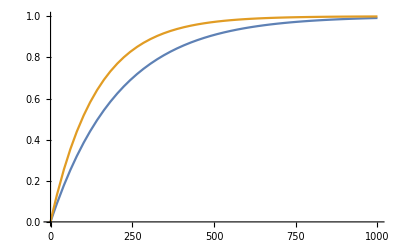

```mathematica
Plot[{Θ[ζ1,ξ],Θ[ζ2,1-ξ]},{s,0,1000}]
```

```mathematica
Θ[ζ1,ξ]
```

1-ⅇ^(-0.006 s)

```mathematica
Export["BernoulliIllust.png",Plot[Table[1-Exp[- E^(z) s],{z,{-5,-2,0,2,5}}],{s,0,10},Filling->Bottom,FillingStyle->Directive[Opacity[0.1],Orange],PlotStyle->Orange,Frame->True,FrameLabel->{"Sales(t-1)","Bernoulli θ","Log[ζ.ξ.ν]=Log[z]={-5,-2,0,2,5}"},LabelStyle->Directive[Bold, Medium],PlotRange->All]]
```

BernoulliIllust.png

```mathematica
Directory[]
```

/home/miglesia